```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
list=FileNames["./output/ctags*.out","",2];
```

```mathematica
data=Import["./output/ctags"<>ToString[100]<>".out","Table"];
```

```mathematica
Sort[DeleteDuplicates[Flatten@data]] //Last
```

5625

```mathematica
M=75^2
```

5625

```mathematica
hue[x_]:=If[x==0,{0,0,0},{Piecewise[{{2-6x, 1/6<x≤2/6}, {0, 2/6<x≤4/6}, {6x-4, 4/6<x≤5/6}, {1, True}}],Piecewise[{{6x, 0/6<x≤1/6}, {1, 1/6<x≤3/6}, {4-6x, 3/6<x≤4/6}, {0, True}}],Piecewise[{{0, 0/6<x≤2/6}, {6x-2, 2/6<x≤3/6}, {6-6x, 5/6<x≤6/6}, {1, True}}]}];
```

```mathematica
permute=RandomSample[Range[M]];
```

```mathematica
changes=Table[i-> permute[[i]],{i,1,M}];
```

```mathematica
permute2=RandomSample[Range[M]];
changes2=Table[i-> permute2[[i]],{i,1,M}];
```

```mathematica
Clear[ColorsReplace]
```

```mathematica
ColorsReplace[x_]:=(ColorsReplace[x]={1,1,1}(0.6(x/.changes)/M+If[x==0,0,0.4])-{0.3,0.3,0.3}hue[(x/.changes2)/M])
```

```mathematica
ColorsReplace[1]
```

{0.617707,0.472587,0.772587}

```mathematica
data=Import["./output/ctags"<>ToString[100#]<>".out","Table"]&/@Range[9];
```

$Aborted

```mathematica
ImageAssemble@Partition[Map[Image[Map[ColorsReplace,#,{2}]ᵀ]&,data],3]
```

-Graphics-

```mathematica
data=Import["./output/ctags"<>ToString[900]<>".out","Table"];
```

```mathematica
Image[Map[ColorsReplace,data[[;;,;;]],{2}]ᵀ]
```

-Graphics-

```mathematica
fibersI=Import["./output/fib.out","Table"];
```

```mathematica
data=Import["./output/ctags900.out","Table"];
```

```mathematica
contsI=Import["./output/contactM901.out","Table"];
```

```mathematica
Export["./output/contactMs.txt",contsI]
```

./output/contactMs.txt

```mathematica
σ=4; proc=0.3;Counts[arr_]:=Module[{uni=DeleteDuplicates[arr]},{Map[Count[arr,#]&,uni],uni}ᵀ];
Replacement[arr_]:=Module[{c=Counts[Flatten@arr]},Sort[c,#1[[1]]>#2[[1]]&]ᵀ[[2,1]]];
RepConts[arr_]:=If[Total[Flatten@arr]<(σ+1)^2 proc,0,1];
```

```mathematica
If[σ==0,
indexes=data;
conts=contsI,
indexes=Table[Replacement[data[[i;;i+σ,j;;j+σ]]],{i,1,Dimensions[data][[1]]-σ,σ+1},{j,1,Dimensions[data][[2]]-σ,σ+1}];
conts=Table[RepConts[contsI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[contsI][[1]]-σ,σ+1},{j,1,Dimensions[contsI][[2]]-σ,σ+1}];
fibers=Table[RepConts[fibersI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[fibersI][[1]]-σ,σ+1},{j,1,Dimensions[fibersI][[2]]-σ,σ+1}]
];
```

```mathematica
{Lx,Ly}=Dimensions[indexes];
```

```mathematica
Invert[x_]:={1,1,1}-x;
```

```mathematica
cells=Map[ColorsReplace,indexes,{2}];
```

```mathematica
BorderQ[x_,i_,j_]:=Module[{n,m,Q=1},
For[n=-1,n≤1,For[m=-1,m≤1,
If[x⟦i+n,j+m⟧≠x⟦i,j⟧,Q=0]
 m++]n++]; Q];
```

```mathematica
outerConts=ArrayPad[Table[If[conts⟦i,j⟧==1,1-BorderQ[indexes,i,j],0],{i,2,Lx-1},{j,2,Ly-1}],1];
```

```mathematica
Image[ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]]
```

-Graphics-

```mathematica
{Lx,Ly}
```

{400,400}

```mathematica
(*indexes=Table[If[i<16&&j<160,1,0],{i,1,64},{j,1,320}];
cells=Map[ColorsReplace,indexes,{2}];
outerConts=Table[If[i==15&&j==159,1,0],{i,1,64},{j,1,320}];
{Lx,Ly}=Dimensions[indexes]*)
```

```mathematica
ThisCell[ind_,x_]:=Map[If[ind==#,1,0]&,x,{2}];NearContactQ[ind_,cellx_,contx_]:=Module[{this,n,m},this=mask ThisCell[ind,cellx]contx;Max@Table[If[this⟦n+R+1,m+R+1⟧==1,1,0],{n,-R,R},{m,-R,R}]];
```

```mathematica
borders=ArrayPad[Table[BorderQ[cells,i,j],{i,2,First@Dimensions[cells]-1},{j,2,Dimensions[cells][[2]]-1}],1];
```

```mathematica
niceCells=(ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]);
```

```mathematica
leaveX=32 12; leaveY = 32 12; shiftx=-5;shifty=-5;
 cutX=Floor[(First@Dimensions[indexes]-leaveX)/2]+1;
cutY=Floor[(Last@Dimensions[indexes]-leaveY)/2]+1;
halfX=If[OddQ[First@Dimensions[indexes]-leaveX],1,0];
halfY=If[OddQ[Last@Dimensions[indexes]-leaveY],1,0];
Image[(niceCells borders+niceCells Map[0.7(1-#)&,borders])⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧]
```

-Graphics-

```mathematica
ind=indexes⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧;
```

```mathematica
endsCut=outerConts⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ;
```

```mathematica
indCut=Map[If[#≠0,1,0]&,indexes⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧,{2}]ᵀ;
```

```mathematica
vertBord=ArrayPad[Map[If[#≠0,1,0]&,ind⟦2;;⟧-ind⟦;;-2⟧,{2}]Map[If[#≠0,1,0]&,ind⟦2;;⟧,{2}]Map[If[#≠0,1,0]&,ind⟦;;-2⟧,{2}],{{1,0},{0,0}}]ᵀ;;vert=ArrayPad[Map[If[#==0,1,0]&,ind⟦2;;⟧-ind⟦;;-2⟧,{2}]Map[If[#≠0,1,0]&,ind⟦2;;⟧,{2}],{{1,0},{0,0}}]ᵀ+2vertBord+vertBord endsCut;
```

```mathematica
horBord=ArrayPad[Map[If[#≠0,1,0]&,ind⟦;;,2;;⟧-ind⟦;;,;;-2⟧,{2}]Map[If[#≠0,1,0]&,ind⟦;;,2;;⟧,{2}]Map[If[#≠0,1,0]&,ind⟦;;,;;-2⟧,{2}],{{0,0},{1,0}}]ᵀ;
hor=ArrayPad[Map[If[#==0,1,0]&,ind⟦;;,2;;⟧-ind⟦;;,;;-2⟧,{2}]Map[If[#≠0,1,0]&,ind⟦;;,2;;⟧,{2}],{{0,0},{1,0}}]ᵀ+2 horBord+horBord endsCut;
```

```mathematica
Image[((vertᵀ)~Join~(horᵀ))/3]
```

-Graphics-

```mathematica
Dimensions@(vert)
```

{384,384}

```mathematica
Gather[Flatten@endsCut][[;;,1]]
```

{0,1}

```mathematica
Gather[Flatten@indCut][[;;,1]]
```

{0,1}

```mathematica
Gather[Flatten@hor][[;;,1]]
```

{0,1,3,2}

```mathematica
filename="./maps/cells.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@indCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(indCutᵀ),"Integer8"];Close[filename]
```

./maps/cells.bin

```mathematica
filename="./maps/dx.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@vert,"Integer32"]; 
BinaryWrite[filename,Flatten@(vertᵀ),"Integer8"];Close[filename]
```

./maps/dx.bin

```mathematica
filename="./maps/dy.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@hor,"Integer32"]; 
BinaryWrite[filename,Flatten@(horᵀ),"Integer8"]; Close[filename]
```

./maps/dy.bin

```mathematica
filename="./maps/na.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@endsCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(endsCutᵀ),"Integer8"]; Close[filename]
```

./maps/na.bin

```mathematica
files=FileNames["../nrvm-discrete/test/*.png"];
filesT=FileNames["../nrvm-discrete/testT/*.png"];
```

```mathematica
mov=Import/@files;
movT=Import/@filesT;
```

```mathematica
dat=ImageData/@mov;
datT=ImageData/@movT;
```

```mathematica
Manipulate[ListPlot[{dat[[t,100,;;]],datT[[t,;;,100]]},PlotRange->{0,0.6}],{t,1,Min[Length@mov,Length@movT],1}]
```

```mathematica
FindFront[arr_]:=Module[{c=Reverse@Map[If[#>0.3,1,0]&,arr]},Length@c-Position[c,1][[1,1]]]
```

```mathematica
front=FindFront[#[[150,;;]]]&/@dat;
frontT=FindFront[#[[;;,200]]]&/@datT;
```

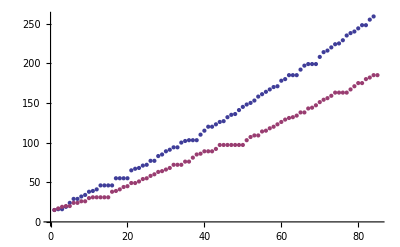

```mathematica
ListPlot[{front,frontT}]
```

```mathematica
Export["./imgs/gif.gif",movT[[;;350]]]
```

./imgs/gif8T.gif

```mathematica
t1=40;t2=76; t3= t2;
vels={LinearModelFit[front[[t1;;t2]],x,x][[1,2,2]],LinearModelFit[frontT[[t1;;t3]],x,x][[1,2,2]]}(12.5 10^-4)/(50 10^-9 10^4)
```

{7.94571,5.59388}

```mathematica
vels[[1]]/vels[[2]]
```

1.42043

```mathematica
Image[Map[1-#&,borders,{2}]]
```

-Graphics-

```mathematica
where=Map[If[#≠0,1,0]&,ind,{2}] ;
```

Table::iterb: Iterator {i, 1, -4 + {} ⟦ 1 ⟧, 5} does not have appropriate bounds.

Part::take: Cannot take positions -78 through 77 in Table[Replacement[data ⟦ i ;; i + σ, j ;; j + σ ⟧], {i, 1, -4 + {} ⟦ 1 ⟧, 5}, {j, 1, Dimensions[data] ⟦ 2 ⟧ - σ, σ + 1}].

Table::itform: Argument (If[#1 ≠ 0, 1, 0] &)[{i, 1, -4 + {} ⟦ 1 ⟧, 5}] at position 2 does not have the correct form for an iterator.

Part::span: i ;; 4 + i is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[$Failed ⟦ i ;; 4 + i, j ;; 4 + j ⟧].

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[0].

Transpose::nmtx: The first two levels of the one-dimensional list {DeleteDuplicates[0], DeleteDuplicates[$Failed ⟦ i ;; 4 + i, j ;; 4 + j ⟧]} cannot be transposed.

Part::partw: Part 2 of Transpose[Transpose[{DeleteDuplicates[0], DeleteDuplicates[$Failed ⟦ i ;; 4 + i, j ;; 4 + j ⟧]}]] does not exist.

```mathematica
Image[where]
```

Image::imgarray: The specified argument If[Transpose[Transpose[{DeleteDuplicates[0], DeleteDuplicates[Part[« 3 »]]}]] ⟦ 2, 1 ⟧ ≠ 0, 1, 0] should be an array of rank 2 or 3 with machine-sized numbers.

Image[If[Transpose[Transpose[{DeleteDuplicates[0],DeleteDuplicates[$Failed⟦i;;4+i,j;;4+j⟧]}]]⟦2,1⟧≠0,1,0]]

-Graphics-

-Graphics-

```mathematica
indexes=Import["./output/ctags"<>ToString[700]<>".out","Table"];
```

Import::nffil: File not found during Import.

```mathematica
borders=ArrayPad[Table[BorderQ[indexes,i,j],{i,2,399},{j,2,399}],1];
```

Part::partd: Part specification $Failed ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 2, 2 ⟧ is longer than depth of object.

Part::partd: Part specification $Failed ⟦ 1, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
InvertONE [x_]:=1-x;
```

```mathematica
Image[Map[ColorsReplace,indexes,{2}]borders+Map[{0,0.1,0.3}#&,InvertONE/@borders,{2}]]
```

Image::imgarray: The specified argument {{{0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, « 32 », {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, {0, 0.1, 0.3}, « 350 »}, « 50 »} should be an array of rank 2 or 3 with machine-sized numbers.

Image[{{{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},«382»,{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3},{0,0.1,0.3}},«399»}]